```mathematica
kv=Import["/Users/perif/Downloads/interpreter2.xml"];
```

```mathematica
nid=Cases[kv,XMLElement["node",{"id"-> id_,"lat"->lat_,"lon"->lng_},_]:>{lat,lng},Infinity];
```

```mathematica
Deg2Num[lat_Real, lon_Real, zoom_Integer] :=  {IntegerPart[(2^(-3 + zoom)*(180 + lon))/45],IntegerPart[2^(-1 + zoom)*(1 - Log[Sec[Degree*lat] + Tan[Degree*lat]]/Pi)]};

Num2Deg[xtile_Integer,ytile_Integer,zoom_Integer]:={ArcTan[Sinh[Pi*(1-2*(ytile/2^zoom))]]/Degree,(xtile/2^zoom)*360-180}//N;

Deg2Tile[lat_Real, lon_Real, zoom_Integer]:=Module[{x,y},{x,y}=Deg2Num[lat,lon,zoom];
"http://tile.openstreetmap.org/"<> IntegerString[zoom]<>"/"<> IntegerString[x]<> "/"<>IntegerString[y]<> ".png"];

Num2Tile[xtile_Integer,ytile_Integer,zoom_Integer]:="http://tile.openstreetmap.org/"<> IntegerString[zoom]<>"/"<> IntegerString[xtile]<> "/"<>IntegerString[ytile]<> ".png";

Tile2Lon[xtile_Integer,zoom_Integer]:=xtile/(2^zoom)*360-180//N;

Tile2Lat[ytile_Integer,zoom_Integer]:= Module[{n},
n=Pi-2*Pi*ytile/(2^zoom);
180/Pi*(ArcTan[0.5*Exp[n]-Exp[-n]])//N
];

Deg2BBoxDeg[lat_Real, lon_Real, zoom_Integer]:=Module[{n},
n=Deg2Num[lat,lon,zoom];
{{Tile2Lat[Last[n],zoom],Tile2Lon[First[n],zoom]},{Tile2Lat[Last[n]+1,zoom],Tile2Lon[First[n]+1,zoom]}}
];

DegList2NumList[degs_List,zoom_Integer]:=Deg2Num[First[#],Last[#],zoom]&/@ degs;

DegList2TileList[degs_List,zoom_Integer]:=Deg2Tile[First[#],Last[#],zoom]&/@ degs;

NumList2TileList[nums_List,zoom_Integer]:=Num2Tile[First[#],Last[#],zoom]&/@ nums;

Clear[DegList2Map];
DegList2Map[degs_List,zoom_Integer,empty_Symbol:False]:=Module[
{numList, tileList,minx,maxx,miny,maxy,x,y,numArray},
numList=DegList2NumList[degs,zoom];
minx=Min[Flatten[First[#]&/@numList]];
maxx=Max[Flatten[First[#]&/@numList]];
miny= Min[Flatten[Last[#]&/@numList]];
maxy= Max[Flatten[Last[#]&/@numList]];
x=maxx-minx;
y=maxy-miny;
Length[numList];
rangex=Range[minx,maxx];
rangey=Range[miny,maxy];
numArray=Flatten[Map[Function[p2,Map[Function[p1,{p1,p2}],rangex]],rangey],1];
dims=ImageDimensions[Import[Num2Tile[First[First[numArray]],Last[First[numArray]],zoom]]];
emptyImage=Image[ConstantArray[1,dims]];
counter=1;
SetSharedVariable[counter];
ParallelEvaluate[last=AbsoluteTime[];localcounter=1;];
getImage = (
localcounter++;If[AbsoluteTime[]-last>1,last=AbsoluteTime[];counter+=localcounter;localcounter=0;];
j=Num2Tile[First[#1],Last[#1],zoom];If[empty||MemberQ[numArray,#1] ,Import[Num2Tile[First[#1],Last[#1],zoom]],emptyImage])&;
imageList=Monitor[
Parallelize[Map[getImage, numArray]],
Row[{ProgressIndicator[Dynamic[counter],{1,First[Dimensions[numArray]]}],,First[StringSplit[ToString[N[counter/(First[Dimensions[numArray]]+1)*100]],"."]]<>"%"}," "]
];
ImageAssemble[Partition[imageList,x+1]]
];
```

```mathematica
x=DegList2Map[{{65.53010989646963,0.},{-26.56505117707799,90.}},6,True]//Timing
```

{17.9087,-Graphics-}

```mathematica
Partition[{{16,8},{17,8},{18,8},{19,8},{20,8},{21,8},{22,8},{23,8},{24,8},{16,9},{17,9},{18,9},{19,9},{20,9},{21,9},{22,9},{23,9},{24,9},{16,10},{17,10},{18,10},{19,10},{20,10},{21,10},{22,10},{23,10},{24,10},{16,11},{17,11},{18,11},{19,11},{20,11},{21,11},{22,11},{23,11},{24,11},{16,12},{17,12},{18,12},{19,12},{20,12},{21,12},{22,12},{23,12},{24,12},{16,13},{17,13},{18,13},{19,13},{20,13},{21,13},{22,13},{23,13},{24,13},{16,14},{17,14},{18,14},{19,14},{20,14},{21,14},{22,14},{23,14},{24,14},{16,15},{17,15},{18,15},{19,15},{20,15},{21,15},{22,15},{23,15},{24,15},{16,16},{17,16},{18,16},{19,16},{20,16},{21,16},{22,16},{23,16},{24,16},{16,17},{17,17},{18,17},{19,17},{20,17},{21,17},{22,17},{23,17},{24,17},{16,18},{17,18},{18,18},{19,18},{20,18},{21,18},{22,18},{23,18},{24,18}},8+1]
```

{{{16,8},{17,8},{18,8},{19,8},{20,8},{21,8},{22,8},{23,8},{24,8}},{{16,9},{17,9},{18,9},{19,9},{20,9},{21,9},{22,9},{23,9},{24,9}},{{16,10},{17,10},{18,10},{19,10},{20,10},{21,10},{22,10},{23,10},{24,10}},{{16,11},{17,11},{18,11},{19,11},{20,11},{21,11},{22,11},{23,11},{24,11}},{{16,12},{17,12},{18,12},{19,12},{20,12},{21,12},{22,12},{23,12},{24,12}},{{16,13},{17,13},{18,13},{19,13},{20,13},{21,13},{22,13},{23,13},{24,13}},{{16,14},{17,14},{18,14},{19,14},{20,14},{21,14},{22,14},{23,14},{24,14}},{{16,15},{17,15},{18,15},{19,15},{20,15},{21,15},{22,15},{23,15},{24,15}},{{16,16},{17,16},{18,16},{19,16},{20,16},{21,16},{22,16},{23,16},{24,16}},{{16,17},{17,17},{18,17},{19,17},{20,17},{21,17},{22,17},{23,17},{24,17}},{{16,18},{17,18},{18,18},{19,18},{20,18},{21,18},{22,18},{23,18},{24,18}}}

```mathematica
w=DegList2Map[{{65.53010989646963,0.},{-26.56505117707799,90.}},2,True];
v=DegList2Map[{{65.53010989646963,0.},{-26.56505117707799,90.}},3,True];
u=DegList2Map[{{65.53010989646963,0.},{-26.56505117707799,90.}},4,True];
t=DegList2Map[{{65.53010989646963,0.},{-26.56505117707799,90.}},5,True];
s=DegList2Map[{{65.53010989646963,0.},{-26.56505117707799,90.}},6,True];
r=DegList2Map[{{65.53010989646963,0.},{-26.56505117707799,90.}},7,True];
```

1 1

{{2,1},{3,1},{2,2},{3,2}}

2 2

{{4,2},{5,2},{6,2},{4,3},{5,3},{6,3},{4,4},{5,4},{6,4}}

4 5

{{8,4},{9,4},{10,4},{11,4},{12,4},{8,5},{9,5},{10,5},{11,5},{12,5},{8,6},{9,6},{10,6},{11,6},{12,6},{8,7},{9,7},{10,7},{11,7},{12,7},{8,8},{9,8},{10,8},{11,8},{12,8},{8,9},{9,9},{10,9},{11,9},{12,9}}

8 10

{{16,8},{17,8},{18,8},{19,8},{20,8},{21,8},{22,8},{23,8},{24,8},{16,9},{17,9},{18,9},{19,9},{20,9},{21,9},{22,9},{23,9},{24,9},{16,10},{17,10},{18,10},{19,10},{20,10},{21,10},{22,10},{23,10},{24,10},{16,11},{17,11},{18,11},{19,11},{20,11},{21,11},{22,11},{23,11},{24,11},{16,12},{17,12},{18,12},{19,12},{20,12},{21,12},{22,12},{23,12},{24,12},{16,13},{17,13},{18,13},{19,13},{20,13},{21,13},{22,13},{23,13},{24,13},{16,14},{17,14},{18,14},{19,14},{20,14},{21,14},{22,14},{23,14},{24,14},{16,15},{17,15},{18,15},{19,15},{20,15},{21,15},{22,15},{23,15},{24,15},{16,16},{17,16},{18,16},{19,16},{20,16},{21,16},{22,16},{23,16},{24,16},{16,17},{17,17},{18,17},{19,17},{20,17},{21,17},{22,17},{23,17},{24,17},{16,18},{17,18},{18,18},{19,18},{20,18},{21,18},{22,18},{23,18},{24,18}}

16 20

{{32,16},{33,16},{34,16},{35,16},{36,16},{37,16},{38,16},{39,16},{40,16},{41,16},{42,16},{43,16},{44,16},{45,16},{46,16},{47,16},{48,16},{32,17},{33,17},{34,17},{35,17},{36,17},{37,17},{38,17},{39,17},{40,17},{41,17},{42,17},{43,17},{44,17},{45,17},{46,17},{47,17},{48,17},{32,18},{33,18},{34,18},{35,18},{36,18},{37,18},{38,18},{39,18},{40,18},{41,18},{42,18},{43,18},{44,18},{45,18},{46,18},{47,18},{48,18},{32,19},{33,19},{34,19},{35,19},{36,19},{37,19},{38,19},{39,19},{40,19},{41,19},{42,19},{43,19},{44,19},{45,19},{46,19},{47,19},{48,19},{32,20},{33,20},{34,20},{35,20},{36,20},{37,20},{38,20},{39,20},{40,20},{41,20},{42,20},{43,20},{44,20},{45,20},{46,20},{47,20},{48,20},{32,21},{33,21},{34,21},{35,21},{36,21},{37,21},{38,21},{39,21},{40,21},{41,21},{42,21},{43,21},{44,21},{45,21},{46,21},{47,21},{48,21},{32,22},{33,22},{34,22},{35,22},{36,22},{37,22},{38,22},{39,22},{40,22},{41,22},{42,22},{43,22},{44,22},{45,22},{46,22},{47,22},{48,22},{32,23},{33,23},{34,23},{35,23},{36,23},{37,23},{38,23},{39,23},{40,23},{41,23},{42,23},{43,23},{44,23},{45,23},{46,23},{47,23},{48,23},{32,24},{33,24},{34,24},{35,24},{36,24},{37,24},{38,24},{39,24},{40,24},{41,24},{42,24},{43,24},{44,24},{45,24},{46,24},{47,24},{48,24},{32,25},{33,25},{34,25},{35,25},{36,25},{37,25},{38,25},{39,25},{40,25},{41,25},{42,25},{43,25},{44,25},{45,25},{46,25},{47,25},{48,25},{32,26},{33,26},{34,26},{35,26},{36,26},{37,26},{38,26},{39,26},{40,26},{41,26},{42,26},{43,26},{44,26},{45,26},{46,26},{47,26},{48,26},{32,27},{33,27},{34,27},{35,27},{36,27},{37,27},{38,27},{39,27},{40,27},{41,27},{42,27},{43,27},{44,27},{45,27},{46,27},{47,27},{48,27},{32,28},{33,28},{34,28},{35,28},{36,28},{37,28},{38,28},{39,28},{40,28},{41,28},{42,28},{43,28},{44,28},{45,28},{46,28},{47,28},{48,28},{32,29},{33,29},{34,29},{35,29},{36,29},{37,29},{38,29},{39,29},{40,29},{41,29},{42,29},{43,29},{44,29},{45,29},{46,29},{47,29},{48,29},{32,30},{33,30},{34,30},{35,30},{36,30},{37,30},{38,30},{39,30},{40,30},{41,30},{42,30},{43,30},{44,30},{45,30},{46,30},{47,30},{48,30},{32,31},{33,31},{34,31},{35,31},{36,31},{37,31},{38,31},{39,31},{40,31},{41,31},{42,31},{43,31},{44,31},{45,31},{46,31},{47,31},{48,31},{32,32},{33,32},{34,32},{35,32},{36,32},{37,32},{38,32},{39,32},{40,32},{41,32},{42,32},{43,32},{44,32},{45,32},{46,32},{47,32},{48,32},{32,33},{33,33},{34,33},{35,33},{36,33},{37,33},{38,33},{39,33},{40,33},{41,33},{42,33},{43,33},{44,33},{45,33},{46,33},{47,33},{48,33},{32,34},{33,34},{34,34},{35,34},{36,34},{37,34},{38,34},{39,34},{40,34},{41,34},{42,34},{43,34},{44,34},{45,34},{46,34},{47,34},{48,34},{32,35},{33,35},{34,35},{35,35},{36,35},{37,35},{38,35},{39,35},{40,35},{41,35},{42,35},{43,35},{44,35},{45,35},{46,35},{47,35},{48,35},{32,36},{33,36},{34,36},{35,36},{36,36},{37,36},{38,36},{39,36},{40,36},{41,36},{42,36},{43,36},{44,36},{45,36},{46,36},{47,36},{48,36}}

32 41

{{64,32},{65,32},{66,32},{67,32},{68,32},{69,32},{70,32},{71,32},{72,32},{73,32},{74,32},{75,32},{76,32},{77,32},{78,32},{79,32},{80,32},{81,32},{82,32},{83,32},{84,32},{85,32},{86,32},{87,32},{88,32},{89,32},{90,32},{91,32},{92,32},{93,32},{94,32},{95,32},{96,32},{64,33},{65,33},{66,33},{67,33},{68,33},{69,33},{70,33},{71,33},{72,33},{73,33},{74,33},{75,33},{76,33},{77,33},{78,33},{79,33},{80,33},{81,33},{82,33},{83,33},{84,33},{85,33},{86,33},{87,33},{88,33},{89,33},{90,33},{91,33},{92,33},{93,33},{94,33},{95,33},{96,33},{64,34},{65,34},{66,34},{67,34},{68,34},{69,34},{70,34},{71,34},{72,34},{73,34},{74,34},{75,34},{76,34},{77,34},{78,34},{79,34},{80,34},{81,34},{82,34},{83,34},{84,34},{85,34},{86,34},{87,34},{88,34},{89,34},{90,34},{91,34},{92,34},{93,34},{94,34},{95,34},{96,34},{64,35},{65,35},{66,35},{67,35},{68,35},{69,35},{70,35},{71,35},{72,35},{73,35},{74,35},{75,35},{76,35},{77,35},{78,35},{79,35},{80,35},{81,35},{82,35},{83,35},{84,35},{85,35},{86,35},{87,35},{88,35},{89,35},{90,35},{91,35},{92,35},{93,35},{94,35},{95,35},{96,35},{64,36},{65,36},{66,36},{67,36},{68,36},{69,36},{70,36},{71,36},{72,36},{73,36},{74,36},{75,36},{76,36},{77,36},{78,36},{79,36},{80,36},{81,36},{82,36},{83,36},{84,36},{85,36},{86,36},{87,36},{88,36},{89,36},{90,36},{91,36},{92,36},{93,36},{94,36},{95,36},{96,36},{64,37},{65,37},{66,37},{67,37},{68,37},{69,37},{70,37},{71,37},{72,37},{73,37},{74,37},{75,37},{76,37},{77,37},{78,37},{79,37},{80,37},{81,37},{82,37},{83,37},{84,37},{85,37},{86,37},{87,37},{88,37},{89,37},{90,37},{91,37},{92,37},{93,37},{94,37},{95,37},{96,37},{64,38},{65,38},{66,38},{67,38},{68,38},{69,38},{70,38},{71,38},{72,38},{73,38},{74,38},{75,38},{76,38},{77,38},{78,38},{79,38},{80,38},{81,38},{82,38},{83,38},{84,38},{85,38},{86,38},{87,38},{88,38},{89,38},{90,38},{91,38},{92,38},{93,38},{94,38},{95,38},{96,38},{64,39},{65,39},{66,39},{67,39},{68,39},{69,39},{70,39},{71,39},{72,39},{73,39},{74,39},{75,39},{76,39},{77,39},{78,39},{79,39},{80,39},{81,39},{82,39},{83,39},{84,39},{85,39},{86,39},{87,39},{88,39},{89,39},{90,39},{91,39},{92,39},{93,39},{94,39},{95,39},{96,39},{64,40},{65,40},{66,40},{67,40},{68,40},{69,40},{70,40},{71,40},{72,40},{73,40},{74,40},{75,40},{76,40},{77,40},{78,40},{79,40},{80,40},{81,40},{82,40},{83,40},{84,40},{85,40},{86,40},{87,40},{88,40},{89,40},{90,40},{91,40},{92,40},{93,40},{94,40},{95,40},{96,40},{64,41},{65,41},{66,41},{67,41},{68,41},{69,41},{70,41},{71,41},{72,41},{73,41},{74,41},{75,41},{76,41},{77,41},{78,41},{79,41},{80,41},{81,41},{82,41},{83,41},{84,41},{85,41},{86,41},{87,41},{88,41},{89,41},{90,41},{91,41},{92,41},{93,41},{94,41},{95,41},{96,41},{64,42},{65,42},{66,42},{67,42},{68,42},{69,42},{70,42},{71,42},{72,42},{73,42},{74,42},{75,42},{76,42},{77,42},{78,42},{79,42},{80,42},{81,42},{82,42},{83,42},{84,42},{85,42},{86,42},{87,42},{88,42},{89,42},{90,42},{91,42},{92,42},{93,42},{94,42},{95,42},{96,42},{64,43},{65,43},{66,43},{67,43},{68,43},{69,43},{70,43},{71,43},{72,43},{73,43},{74,43},{75,43},{76,43},{77,43},{78,43},{79,43},{80,43},{81,43},{82,43},{83,43},{84,43},{85,43},{86,43},{87,43},{88,43},{89,43},{90,43},{91,43},{92,43},{93,43},{94,43},{95,43},{96,43},{64,44},{65,44},{66,44},{67,44},{68,44},{69,44},{70,44},{71,44},{72,44},{73,44},{74,44},{75,44},{76,44},{77,44},{78,44},{79,44},{80,44},{81,44},{82,44},{83,44},{84,44},{85,44},{86,44},{87,44},{88,44},{89,44},{90,44},{91,44},{92,44},{93,44},{94,44},{95,44},{96,44},{64,45},{65,45},{66,45},{67,45},{68,45},{69,45},{70,45},{71,45},{72,45},{73,45},{74,45},{75,45},{76,45},{77,45},{78,45},{79,45},{80,45},{81,45},{82,45},{83,45},{84,45},{85,45},{86,45},{87,45},{88,45},{89,45},{90,45},{91,45},{92,45},{93,45},{94,45},{95,45},{96,45},{64,46},{65,46},{66,46},{67,46},{68,46},{69,46},{70,46},{71,46},{72,46},{73,46},{74,46},{75,46},{76,46},{77,46},{78,46},{79,46},{80,46},{81,46},{82,46},{83,46},{84,46},{85,46},{86,46},{87,46},{88,46},{89,46},{90,46},{91,46},{92,46},{93,46},{94,46},{95,46},{96,46},{64,47},{65,47},{66,47},{67,47},{68,47},{69,47},{70,47},{71,47},{72,47},{73,47},{74,47},{75,47},{76,47},{77,47},{78,47},{79,47},{80,47},{81,47},{82,47},{83,47},{84,47},{85,47},{86,47},{87,47},{88,47},{89,47},{90,47},{91,47},{92,47},{93,47},{94,47},{95,47},{96,47},{64,48},{65,48},{66,48},{67,48},{68,48},{69,48},{70,48},{71,48},{72,48},{73,48},{74,48},{75,48},{76,48},{77,48},{78,48},{79,48},{80,48},{81,48},{82,48},{83,48},{84,48},{85,48},{86,48},{87,48},{88,48},{89,48},{90,48},{91,48},{92,48},{93,48},{94,48},{95,48},{96,48},{64,49},{65,49},{66,49},{67,49},{68,49},{69,49},{70,49},{71,49},{72,49},{73,49},{74,49},{75,49},{76,49},{77,49},{78,49},{79,49},{80,49},{81,49},{82,49},{83,49},{84,49},{85,49},{86,49},{87,49},{88,49},{89,49},{90,49},{91,49},{92,49},{93,49},{94,49},{95,49},{96,49},{64,50},{65,50},{66,50},{67,50},{68,50},{69,50},{70,50},{71,50},{72,50},{73,50},{74,50},{75,50},{76,50},{77,50},{78,50},{79,50},{80,50},{81,50},{82,50},{83,50},{84,50},{85,50},{86,50},{87,50},{88,50},{89,50},{90,50},{91,50},{92,50},{93,50},{94,50},{95,50},{96,50},{64,51},{65,51},{66,51},{67,51},{68,51},{69,51},{70,51},{71,51},{72,51},{73,51},{74,51},{75,51},{76,51},{77,51},{78,51},{79,51},{80,51},{81,51},{82,51},{83,51},{84,51},{85,51},{86,51},{87,51},{88,51},{89,51},{90,51},{91,51},{92,51},{93,51},{94,51},{95,51},{96,51},{64,52},{65,52},{66,52},{67,52},{68,52},{69,52},{70,52},{71,52},{72,52},{73,52},{74,52},{75,52},{76,52},{77,52},{78,52},{79,52},{80,52},{81,52},{82,52},{83,52},{84,52},{85,52},{86,52},{87,52},{88,52},{89,52},{90,52},{91,52},{92,52},{93,52},{94,52},{95,52},{96,52},{64,53},{65,53},{66,53},{67,53},{68,53},{69,53},{70,53},{71,53},{72,53},{73,53},{74,53},{75,53},{76,53},{77,53},{78,53},{79,53},{80,53},{81,53},{82,53},{83,53},{84,53},{85,53},{86,53},{87,53},{88,53},{89,53},{90,53},{91,53},{92,53},{93,53},{94,53},{95,53},{96,53},{64,54},{65,54},{66,54},{67,54},{68,54},{69,54},{70,54},{71,54},{72,54},{73,54},{74,54},{75,54},{76,54},{77,54},{78,54},{79,54},{80,54},{81,54},{82,54},{83,54},{84,54},{85,54},{86,54},{87,54},{88,54},{89,54},{90,54},{91,54},{92,54},{93,54},{94,54},{95,54},{96,54},{64,55},{65,55},{66,55},{67,55},{68,55},{69,55},{70,55},{71,55},{72,55},{73,55},{74,55},{75,55},{76,55},{77,55},{78,55},{79,55},{80,55},{81,55},{82,55},{83,55},{84,55},{85,55},{86,55},{87,55},{88,55},{89,55},{90,55},{91,55},{92,55},{93,55},{94,55},{95,55},{96,55},{64,56},{65,56},{66,56},{67,56},{68,56},{69,56},{70,56},{71,56},{72,56},{73,56},{74,56},{75,56},{76,56},{77,56},{78,56},{79,56},{80,56},{81,56},{82,56},{83,56},{84,56},{85,56},{86,56},{87,56},{88,56},{89,56},{90,56},{91,56},{92,56},{93,56},{94,56},{95,56},{96,56},{64,57},{65,57},{66,57},{67,57},{68,57},{69,57},{70,57},{71,57},{72,57},{73,57},{74,57},{75,57},{76,57},{77,57},{78,57},{79,57},{80,57},{81,57},{82,57},{83,57},{84,57},{85,57},{86,57},{87,57},{88,57},{89,57},{90,57},{91,57},{92,57},{93,57},{94,57},{95,57},{96,57},{64,58},{65,58},{66,58},{67,58},{68,58},{69,58},{70,58},{71,58},{72,58},{73,58},{74,58},{75,58},{76,58},{77,58},{78,58},{79,58},{80,58},{81,58},{82,58},{83,58},{84,58},{85,58},{86,58},{87,58},{88,58},{89,58},{90,58},{91,58},{92,58},{93,58},{94,58},{95,58},{96,58},{64,59},{65,59},{66,59},{67,59},{68,59},{69,59},{70,59},{71,59},{72,59},{73,59},{74,59},{75,59},{76,59},{77,59},{78,59},{79,59},{80,59},{81,59},{82,59},{83,59},{84,59},{85,59},{86,59},{87,59},{88,59},{89,59},{90,59},{91,59},{92,59},{93,59},{94,59},{95,59},{96,59},{64,60},{65,60},{66,60},{67,60},{68,60},{69,60},{70,60},{71,60},{72,60},{73,60},{74,60},{75,60},{76,60},{77,60},{78,60},{79,60},{80,60},{81,60},{82,60},{83,60},{84,60},{85,60},{86,60},{87,60},{88,60},{89,60},{90,60},{91,60},{92,60},{93,60},{94,60},{95,60},{96,60},{64,61},{65,61},{66,61},{67,61},{68,61},{69,61},{70,61},{71,61},{72,61},{73,61},{74,61},{75,61},{76,61},{77,61},{78,61},{79,61},{80,61},{81,61},{82,61},{83,61},{84,61},{85,61},{86,61},{87,61},{88,61},{89,61},{90,61},{91,61},{92,61},{93,61},{94,61},{95,61},{96,61},{64,62},{65,62},{66,62},{67,62},{68,62},{69,62},{70,62},{71,62},{72,62},{73,62},{74,62},{75,62},{76,62},{77,62},{78,62},{79,62},{80,62},{81,62},{82,62},{83,62},{84,62},{85,62},{86,62},{87,62},{88,62},{89,62},{90,62},{91,62},{92,62},{93,62},{94,62},{95,62},{96,62},{64,63},{65,63},{66,63},{67,63},{68,63},{69,63},{70,63},{71,63},{72,63},{73,63},{74,63},{75,63},{76,63},{77,63},{78,63},{79,63},{80,63},{81,63},{82,63},{83,63},{84,63},{85,63},{86,63},{87,63},{88,63},{89,63},{90,63},{91,63},{92,63},{93,63},{94,63},{95,63},{96,63},{64,64},{65,64},{66,64},{67,64},{68,64},{69,64},{70,64},{71,64},{72,64},{73,64},{74,64},{75,64},{76,64},{77,64},{78,64},{79,64},{80,64},{81,64},{82,64},{83,64},{84,64},{85,64},{86,64},{87,64},{88,64},{89,64},{90,64},{91,64},{92,64},{93,64},{94,64},{95,64},{96,64},{64,65},{65,65},{66,65},{67,65},{68,65},{69,65},{70,65},{71,65},{72,65},{73,65},{74,65},{75,65},{76,65},{77,65},{78,65},{79,65},{80,65},{81,65},{82,65},{83,65},{84,65},{85,65},{86,65},{87,65},{88,65},{89,65},{90,65},{91,65},{92,65},{93,65},{94,65},{95,65},{96,65},{64,66},{65,66},{66,66},{67,66},{68,66},{69,66},{70,66},{71,66},{72,66},{73,66},{74,66},{75,66},{76,66},{77,66},{78,66},{79,66},{80,66},{81,66},{82,66},{83,66},{84,66},{85,66},{86,66},{87,66},{88,66},{89,66},{90,66},{91,66},{92,66},{93,66},{94,66},{95,66},{96,66},{64,67},{65,67},{66,67},{67,67},{68,67},{69,67},{70,67},{71,67},{72,67},{73,67},{74,67},{75,67},{76,67},{77,67},{78,67},{79,67},{80,67},{81,67},{82,67},{83,67},{84,67},{85,67},{86,67},{87,67},{88,67},{89,67},{90,67},{91,67},{92,67},{93,67},{94,67},{95,67},{96,67},{64,68},{65,68},{66,68},{67,68},{68,68},{69,68},{70,68},{71,68},{72,68},{73,68},{74,68},{75,68},{76,68},{77,68},{78,68},{79,68},{80,68},{81,68},{82,68},{83,68},{84,68},{85,68},{86,68},{87,68},{88,68},{89,68},{90,68},{91,68},{92,68},{93,68},{94,68},{95,68},{96,68},{64,69},{65,69},{66,69},{67,69},{68,69},{69,69},{70,69},{71,69},{72,69},{73,69},{74,69},{75,69},{76,69},{77,69},{78,69},{79,69},{80,69},{81,69},{82,69},{83,69},{84,69},{85,69},{86,69},{87,69},{88,69},{89,69},{90,69},{91,69},{92,69},{93,69},{94,69},{95,69},{96,69},{64,70},{65,70},{66,70},{67,70},{68,70},{69,70},{70,70},{71,70},{72,70},{73,70},{74,70},{75,70},{76,70},{77,70},{78,70},{79,70},{80,70},{81,70},{82,70},{83,70},{84,70},{85,70},{86,70},{87,70},{88,70},{89,70},{90,70},{91,70},{92,70},{93,70},{94,70},{95,70},{96,70},{64,71},{65,71},{66,71},{67,71},{68,71},{69,71},{70,71},{71,71},{72,71},{73,71},{74,71},{75,71},{76,71},{77,71},{78,71},{79,71},{80,71},{81,71},{82,71},{83,71},{84,71},{85,71},{86,71},{87,71},{88,71},{89,71},{90,71},{91,71},{92,71},{93,71},{94,71},{95,71},{96,71},{64,72},{65,72},{66,72},{67,72},{68,72},{69,72},{70,72},{71,72},{72,72},{73,72},{74,72},{75,72},{76,72},{77,72},{78,72},{79,72},{80,72},{81,72},{82,72},{83,72},{84,72},{85,72},{86,72},{87,72},{88,72},{89,72},{90,72},{91,72},{92,72},{93,72},{94,72},{95,72},{96,72},{64,73},{65,73},{66,73},{67,73},{68,73},{69,73},{70,73},{71,73},{72,73},{73,73},{74,73},{75,73},{76,73},{77,73},{78,73},{79,73},{80,73},{81,73},{82,73},{83,73},{84,73},{85,73},{86,73},{87,73},{88,73},{89,73},{90,73},{91,73},{92,73},{93,73},{94,73},{95,73},{96,73}}

```mathematica
ImageAssemble[Partition[v,9]]
```

-Graphics-

```mathematica
Partition[Flatten[v],18]
```

{{16,8,17,8,18,8,19,8,20,8,21,8,22,8,23,8,24,8},{16,9,17,9,18,9,19,9,20,9,21,9,22,9,23,9,24,9},{16,10,17,10,18,10,19,10,20,10,21,10,22,10,23,10,24,10},{16,11,17,11,18,11,19,11,20,11,21,11,22,11,23,11,24,11},{16,12,17,12,18,12,19,12,20,12,21,12,22,12,23,12,24,12},{16,13,17,13,18,13,19,13,20,13,21,13,22,13,23,13,24,13},{16,14,17,14,18,14,19,14,20,14,21,14,22,14,23,14,24,14},{16,15,17,15,18,15,19,15,20,15,21,15,22,15,23,15,24,15},{16,16,17,16,18,16,19,16,20,16,21,16,22,16,23,16,24,16},{16,17,17,17,18,17,19,17,20,17,21,17,22,17,23,17,24,17},{16,18,17,18,18,18,19,18,20,18,21,18,22,18,23,18,24,18}}

```mathematica
v
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dimensions[v]
```

```mathematica
{99,2}
```

```mathematica
Deg2BBoxDeg[45.7352355,5.0355499,10]
```

{{39.5729,4.92188},{39.2296,5.27344}}

```mathematica
Flatten[First[%]]
```

{39.5729,4.92188}

```mathematica
Deg2BBoxTile[45.7352355,5.0355499,2]
```

{{1,2},{2,3}}

```mathematica
{Import[Deg2Tile[65.53010989646963,0.,2]],Import[Deg2Tile[-26.56505117707799,90.,2]]}
```

{-Graphics-,-Graphics-}

```mathematica
Tile2Lat[365,10]
```

39.5729

```mathematica
Tile2Long[526,10]
```

4.92188

```mathematica
Last[First[nid]]
```

5.0355499

```mathematica
First[First[nid]]
```

45.7352355

```mathematica
"45.7352355"
First[nid]
```

45.7352355

```mathematica
{"45.7352355","5.0355499"}
```

{45.7352355,5.0355499}

```mathematica
Deg2Num[ToExpression[First[First[nid]]],ToExpression[Last[First[nid]]],10]
```

{526,365}

```mathematica
{IntegerPart[(128 (180+"5.0355499"))/45],IntegerPart[512 (1-Log[Sec["45.7352355" °]+Tan["45.7352355" °]]/π)]}
```

{IntegerPart[(128 (180+5.0355499))/45],IntegerPart[512 (1-Log[Sec[45.7352355 °]+Tan[45.7352355 °]]/π)]}

```mathematica
Deg2BBoxDeg[45.7352355,5.0355499,10]
```

{{39.5729,4.92188},{39.2296,4.57031}}

```mathematica
Take[nid,10]
```

{{45.7352355,5.0355499},{45.7400960,5.0353143},{45.7303618,5.0356982},{45.7229478,5.0285298},{45.7264531,5.0318951},{45.7194968,5.0252402},{45.7163838,5.0222057},{45.7129418,5.0189084},{45.7095898,5.0156373},{45.7037235,5.0099956}}

```mathematica
Deg2Num[ToExpression[First[#1]],ToExpression[Last[#1]],14]&/@Take[nid,10]
```

{{8421,5846},{8421,5845},{8421,5846},{8420,5846},{8421,5846},{8420,5847},{8420,5847},{8420,5847},{8420,5847},{8420,5848}}

```mathematica
{ToExpression[First[#]],ToExpression[Last[#]]}&/@Take[nid,10]
```

{{45.7352,5.03555},{45.7401,5.03531},{45.7304,5.0357},{45.7229,5.02853},{45.7265,5.0319},{45.7195,5.02524},{45.7164,5.02221},{45.7129,5.01891},{45.7096,5.01564},{45.7037,5.01}}

```mathematica
zzzz=Import[Deg2Tile[45.7352355,5.0355499,2]];
```

```mathematica
ImageDimensions[zzzz]
```

```mathematica
Image[ConstantArray[1,{256,256}]]
```

-Graphics-

```mathematica
kv[[2]][[3]][[]]
```

{XMLElement[note,{},{The data included in this document is from www.openstreetmap.org. The data is made available under ODbL.}],XMLElement[meta,{osm_base→2013-12-27T22:47:01Z},{}],«29567»,XMLElement[node,{id→2588296445,lat→50.2192523,lon→2.5974619},{}],XMLElement[node,{id→2589210068,lat→43.2966802,lon→5.9628310},{}]}

```mathematica
nodes=Cases[kv,XMLElement["way",{"id"-> id_},x__]:>{id,x},Infinity];
```

```mathematica
Length[nodes]
```

1936

```mathematica
First@nodes
```

{5212612,{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}}

```mathematica
getColors=Cases[nodes,{_,XMLElement["nd",{"ref"->x_},_]:>x},Infinity]
```

```mathematica
First[nodes]
```

{5212612,{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}}

```mathematica
Rest[First[nodes]]
```

{{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}}

```mathematica
Flatten[Rest[First[nodes]],1]
```

{XMLElement[nd,{ref→1196065838},{}],XMLElement[nd,{ref→1196066023},{}],XMLElement[nd,{ref→208943111},{}]}

```mathematica
First[Flatten[Rest[First[nodes]],1]]
```

XMLElement[nd,{ref→1196065838},{}]

```mathematica
ConnectorNodes[cnodes_]:=Cases[cnodes,XMLElement[_,{"ref"->x_},_]:>x,Infinity]
```

```mathematica
connectorNodes[Flatten[Rest[First[nodes]],1]]
```

{1196065838,1196066023,208943111}

```mathematica
getColors=Cases[Flatten[Rest[First[nodes]],1],XMLElement[_,{"ref"->x_},_]:>x,Infinity]
```

```mathematica
ConnectedNodes[cnodes_]:=Cases[cnodes,XMLElement[_,{"ref"->x_},_]:>x,Infinity]
```

```mathematica
NodesAndConnections[nlist_]:={First[nlist],ConnectorNodes[Rest[nlist]]};
```

```mathematica
NodesAndConnections /@ nodes
```

{{5212612,{1196065838,1196066023,208943111}},{21624881,{258576956,1606752560,1606752570,1606752565,582472544}},{22873851,{245917040,245917041,245917042}},{23194663,{250837716,250837717,250837220,250837221,250837338,250837405,250838031,250838071,250838212,250838625,250838474,253995184,253995185,253995735,253995870,253996383,253996593,253996696,253997579}},«1929»,{244487341,{2517995589,2517995586,2517995584}},{244487347,{2517995578,2517995573,2517995569}},{249828252,{2130939220,2563785952}}}

```mathematica
NodesAndConnections[First[nodes]]
```

{5212612,{1196065838,1196066023,208943111}}

```mathematica
KVNetwork[kvfile_]:=Module[{NodesAndConnections,nodes,kv},
NodesAndConnections[nlist_]:={First[nlist],ConnectorNodes[Rest[nlist]]};
kv=Import[kvfile];
nodes=Cases[kv,XMLElement["way",{"id"-> id_},x__]:>{id,x},Infinity];
NodesAndConnections/@nodes
]
```

```mathematica
nodes=KVNetwork["/Users/perif/Downloads/interpreter.xml"];
```

```mathematica
RuleCreator[nlist_]:=Module[{},
head=First[nlist];
queue=Flatten[Rest[nlist]];
head -> #&/@queue
]
```

```mathematica
adjList=Flatten[RuleCreator /@nodes];
```

```mathematica
adjList,DirectedEdges->False];
g=Show[gplot,ImageSize->2000];
```

```mathematica
Export["~/Desktop/ggraph.png",g];
```

```mathematica
Show[%155,ImageSize->Large]
```

```mathematica
kqv=KVNetwork[Import["http://oapi-fr.openstreetmap.fr/oapi/interpreter?data=[out:xml];way[%22voltage%22=%22400000%22][%22power%22=%22line%22][%22line%22!=%22busbar%22];out%20skel;%3E;out%20skel;"]];
```

Import::nffil: File not found during Import.

Import::chtype: First argument {} is not a valid file, directory, or URL specification.

{}

```mathematica
gplot=GraphPlot[Flatten[RuleCreator /@KVNetwork["/Users/perif/Downloads/interpreter2.xml"]],DirectedEdges->False];
```

```mathematica
g=Show[gplot,ImageSize->2000];
```

```mathematica
Export["~/Desktop/ggraph4.png",g];
```

```mathematica
WorldPl
```

```mathematica
<<WorldPlot`
```

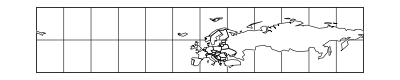

```mathematica
WorldPlot[Europe]
```

```mathematica
Head[True]
```

Symbol